## Subradiance-protected excitation spreading for collimated photon emission

See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

## setup

```mathematica
(*PHYSICAL CONSTANTS*)
ℏ = 6.62607015*^-34/(2π);
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
atomnum = 16;
J = 1; (*upper level total angular momentum*) 
λ = 7.8*10^-7;
k =2π/λ;
(*matelem = the reduced matrix element
γ = matelem^2 k^3/(6 π ℏ ϵ0);*) (*single two-level atom linewidth*)
a=0.7 λ; (*atomic grid spatial period*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
deg = 2J+1;
dim = deg*atomnum; (*Hamiltonian shape is dim x dim*)
Hfull = Array[Subscript[H, ##]&,{dim,dim}];
(*FUNCTIONS*)
Subscript[r, i_,j_]=a{Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->atomnum;(*distance between atoms i,j*)
sphrWave[x_,y_,z_]=(ⅇ^(ⅈ k √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2));(*spherical wave*)
Subscript[Kδ, μ_,ν_]:=KroneckerDelta[SymbolName[μ],SymbolName[ν]];(*symbolic Kronecker delta*)
dipOp[α_,β_]=(D[#,α]D[#,β]-Subscript[Kδ, α,β] Laplacian[#,{x,y,z}]-Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])&; (*derivative op in the expression for positive freq. component of monochromatic dipole radation*)
Subscript[G, α_,β_]:=dipOp[α,β][sphrWave[x,y,z]];(*element (α,β) of the positive frequency compenent of monochromatic dip. radiation*)
GTensor = Table[Subscript[G, α,β]+(Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])/3,{α,{x,y,z}},{β,{x,y,z}}];
Subscript[e, μ_] := {1/(√2){1,0,-ⅈ 1},{1,0,0},1/(√2){1,0,+ⅈ 1}}[[μ]];(*polarization basis. μ=1,2,3 -> polarization σ=-1,0,+1 *)
GTensorSph = Table[Subscript[e, n]*.GTensor.Subscript[e, m],{n,Range[3]},{m,Range[3]}]; (*GTensor in spherical basis*)
Subscript[dipRadKernel, μ_,ν_,i_,j_]:=GTensorSph[[μ,ν]]/.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> Subscript[r, i,j]/.{x-> u[[1]],y->u[[2]],z-> 0}/.u-> Subscript[r, i,j] (*element (μ,ν) of the dipole radiation kernel between atoms i,j*)
```

TESTING FUNCTIONS, etc

```mathematica
Subscript[dipRadKernel, 1,1,1,2]
```

7.12943×10^23-1.30621×10^23 ⅈ

```mathematica
Subscript[testkernel, 1,1,1,2]
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

Part::partd: Part specification u⟦2⟧ is longer than depth of object.

7.12943×10^23-1.30621×10^23 ⅈ

```mathematica
Piecewise[{{0,1≠1},{1,1==1}}]
```

1

```mathematica
pw[1,0]
```

0

Hamiltonian matrix elements: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), where μ,ν specify polarization projections and j,k are the atom indices in the 2D grid.

TODO: 
- find what values the paper used for Δ,γ, then build those into the Hamiltonian. 
- add in initial excitation as the paper does

## run

```mathematica
(*fill the Hamiltonian*)
For[i=1,i<Length[atomnum]+1,i++,
For[j=1,j<Length[atomnum]+1,j++,
For[ν=1,ν<Length[pol]+1,ν++,
For[μ=1,μ<Length[pol]+1,μ++,
G = (6 π γ)/k^3 Subscript[dipRadKernel, μ,ν,i,j]; (*this currently has a Kronecker delta, and so evaluates to an indeterminate expression. may give problems to the numerical solver. may need a piecewise expression here*)
Ωμνij=Re[G];
γμνij =Im[G];
Hfull[[3(i-1)+ν,3(j-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij;
]
]
]
]
```

## random tests

Check my grid mapping. 2D grid, but only one index to specify atoms

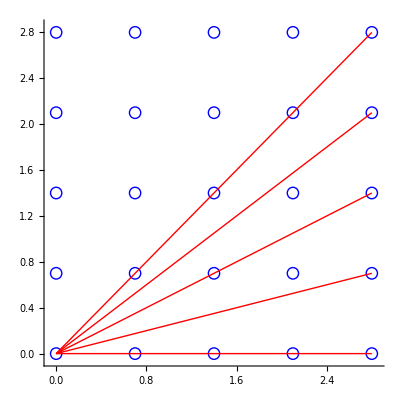

```mathematica
num=5;
a=0.7;
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
Show[Table[Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],{i,Range[num^2]}],Table[r[1,j],{j,{5,10,15,20,25}}],Axes->True]
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}